# The New Seeker

Brian Beckman
9 Aug 2019

## Sampling

## Uniform in d-Ball—2 [ n, d ]

```mathematica
ClearAll[uniformInBall2];
uniformInBall2[n_:50000,d_:2]:=
Drop[#,2]&/@
Normalize/@
RandomVariate[
NormalDistribution[],{n,d+2}];
```

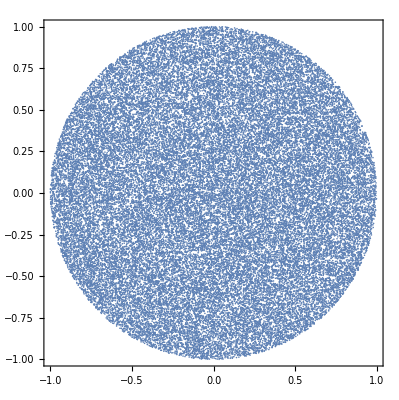

```mathematica
ListPlot[uniformInBall2[],AspectRatio->Automatic,Frame->True]
```

## Seeking

## Visualizing

```mathematica
ClearAll[getTarget];
getTarget[d_:4]:=uniformInBall2[1,d]⟦1⟧;
```

```mathematica
ClearAll[prtSeek2D,vizSeek2D,nexter,echo];
nexter[{yp_,_,cov_,_},{t_,decay_,i_}]:=
Module[{σ=Sqrt[cov],a,b,da,db},
a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
da=EuclideanDistance[t,a];
db=EuclideanDistance[t,b];
With[{νcov=Quiet[cov*decay]},
If[da<db,
{a,da,νcov,i},
{b,db,νcov,i}]]];
```

```mathematica
ClearAll[picker,dist,yp,cov,i];
picker[n_]:=#⟦n⟧&;
(* getter fns *) {yp,dist,cov,i}=picker/@Range[4];
echo=Echo;
DBALLRADIUS=1.0;
vizSeek2D[tol_:0.1,dec_:0.992,maxIt_:10000,pr_:10,dim_:2]:=
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{decimator={indexer[yp[#]],dist[#],cov[#],i[#]}&},
With[{big=100(* so TakeWhile won't truncate results *),tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{all=FoldList[nexter,{ini,big,DBALLRADIUS^2,0},Table[{tar,dec,i},{i,maxIt}]]},
With[{surv=TakeWhile[all,(*True&*)(dist[#]>tol)&]},
With[{sampled=decimator/@surv,lsurv=Length[surv]-1},
Show[Graphics[{LightGray,Disk[],White,Disk[indexer@tar,0.3],Black,Circle[indexer@tar,0.3],
{Hue[(2.+i[#]*4/lsurv)/6.],Circle[yp[#],Sqrt[cov[#]]],Point[yp[#]]}&/@sampled,
Text[Style[lsurv,"Text",Background->White],{-pr/2,pr*0.90}]
}],AspectRatio->Automatic,Frame->True,PlotRange->1.025*pr]]]]]]]];
Manipulate[
vizSeek2D[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,2,"log_10(reps)"},0,5,0.25,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

## Bisecting for the Decay

For each dim, tol, maxIter, find, via bisection, the decay Δ that converges a search in the smallest number of trials. Do so statistically over lRollout trials in a rollout. 

A bad search can die or it can wander. (The following sentence is wrong; this is not a good definition of dead, because iterated 6-σ searches may bring it closer!) A search dies when its center yp is six sigma away from tar; the chances that new a/b guesses will get closer to tar are negligibly small. A search wanders when it fails to converge within tol after maxIter trials; it runs out of gas looking. To find out whether a search wanders, we must follow it to the bitter end (that’s expensive). 

Here is a version of nexter that throws when it dies or wins (to avoid wasting computation after death) or wanders (for structural uniformity in the two failure cases). It decays σ rather than covariance (it’s a continuing ambiguity in this research program whether to decay σ or σ^2). It may not matter, it might matter; I don’t know yet.

```mathematica
ClearAll[nexter002];
nexter002[{yp_,dist_,σ_},{tar_,Δ_,tol_,maxIter_,i_}]:=
(* 8 parameters; account for all of them: *)
Module[{a,b,da,db,d},
(* (2) dist, σ used *)
If[(dist>10maxIter σ),Throw[{yp,dist,σ,tar,Δ,i},"Dead"]];
(* (4) maxIter, i used *)
If[i≥maxIter,Throw[{yp,dist,σ,tar,Δ,i},"Wandering"]]; 
(* (5) yp used *)
a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
(* (6) tar used *)
da=EuclideanDistance[tar,a];
(* (7) tol used *)
If[da<tol,Throw[{a,da,σ,tar,Δ,i},"Found"]];
db=EuclideanDistance[tar,b];
If[da<tol,Throw[{b,db,σ,tar,Δ,i},"Found"]];
(* (8) Δ used *)
With[{νσ=Quiet[σ*Δ]},
Sow@If[da<db,
{a,da,νσ},
{b,db,νσ}]]];
```

```mathematica
ClearAll[trialDict];
trialDict[{yp_,dist_,σ_,tar_,Δ_,i_},tag_]:=
<|"yp"->yp,"dist"->dist,"σ"->σ,"tar"->tar,"Δ"->Δ,"i"->i,"tag"->tag|>;
```

```mathematica
ClearAll[vizSeek2D,vizSeek2D002,dist,yp,σ,cov,i];
picker[n_]:=#⟦n⟧&;{yp,dist,σ}=picker/@Range[3];
echo=Echo;
DBALLRADIUS=1.0;
vizSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{result=Reap[Catch[Catch[Catch[Fold[
nexter002,{ini,0,DBALLRADIUS},
Table[{tar,Δ,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]
]},
With[{tag=result⟦1⟧["tag"],points=result⟦2,1⟧,smtar=indexer@tar,sampled=sampler/@result⟦2,1⟧,l=Length[result⟦2,1⟧]},
Show[Graphics[{
LightGray,Disk[],White,Disk[smtar,0.3],Black,Circle[smtar,0.3],
MapIndexed[
{Hue[(2.+#2*4/l)/6.],Circle[yp[#1],σ[#1]],Point[yp[#1]]}&,
sampled],
Text[Style[{l,tag,Δ,tol,σ[Last[sampled]]tol},"Text",Background->White],{0,pr*0.960}]
}],AspectRatio->Automatic,Frame->True,PlotRange->1.025*pr]]]]]]];
Manipulate[
vizSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

```mathematica
ClearAll[cume,zeroStats];
zeroStats=<|"mean"->0,"min"->Infinity,"max"->-Infinity,"var"->0,"n"->0,"stddev"->0|>;
cume[runningStats_,z_]:=
With[{
m=runningStats["mean"],
max=runningStats["max"],
min=runningStats["min"],
n=runningStats["n"],
var=runningStats["var"]},
With[{K=1./(n+1.),r=z-m},
With[{var2=((n-1)var+K n r^2)/Max[1,n]},
<|"mean"->m+K r,"n"->n+1,"min"->Min[z,min],
"max"->Max[z,max],"var"->var2,"stddev"->Sqrt[var2]|>]]];
(*FoldList[cume,zeroStats,{55,89,144}]*)
```

```mathematica
ClearAll[trial];
trial[tar_,Δ_,tol_,maxIter_]:=
Module[{tagg},
With[{dim=Length[tar]},
Reap[Catch[Catch[Catch[
Fold[nexter002,
{ConstantArray[0.,dim],0.,1.},
Table[{tar,Δ,tol,maxIter,i},{i,maxIter}]],
"Found",f],"Dead",f],"Wandering",f]
]]⟦2,1⟧];
trial[getTarget[2],.9599,0.01,1000]
```

{{{0.679165,-0.36296},0.489215,0.9599},{{1.26771,-1.41831},1.45072,0.921408},{{0.87432,-0.75444},0.771858,0.88446},{{0.170042,0.297374},0.878172,0.848993},{{0.681443,0.395874},0.501783,0.814948},{{1.20924,1.23664},1.24721,0.782269},{{0.376461,0.832596},1.03372,0.7509},{{-0.0938602,1.02761},1.49506,0.720789},{{0.754285,1.01452},1.03651,0.691885},{{0.560202,0.173005},0.468971,0.66414},{{0.619825,-0.255616},0.46134,0.637508},{{-0.0761093,0.654872},1.25501,0.611944},{{0.785376,0.982067},0.997889,0.587405},{{1.24438,1.13656},1.15563,0.56385},{{0.927122,0.653257},0.649941,0.54124},{{1.05329,0.404405},0.400816,0.519536},{{1.50013,0.452677},0.670507,0.498703},{{0.978863,-0.0515312},0.0621506,0.478705},{{1.67995,-0.256269},0.73025,0.459509},{{1.68645,-0.168334},0.709605,0.441083},{{2.07622,0.391451},1.14374,0.423395},{{2.18741,0.11154},1.19305,0.406417},{{2.18416,-0.342239},1.23571,0.39012},{{1.5326,0.0332406},0.534311,0.374476},{{1.64354,0.282271},0.700823,0.359459},{{1.68944,0.333917},0.763868,0.345045},{{1.65954,0.311285},0.72721,0.331209},{{1.57482,0.214323},0.611978,0.317927},{{1.21287,0.0369213},0.215992,0.305178},{{1.20922,-0.0449703},0.216699,0.292941},{{0.87599,0.0309129},0.125179,0.281194},{{0.884049,-0.120207},0.171615,0.269918},{{0.854534,-0.0183744},0.14665,0.259094},{{1.16935,-0.360421},0.40529,0.248705},{{0.86092,-0.182018},0.234272,0.238731},{{0.774459,-0.414708},0.477984,0.229158},{{1.2022,-0.362009},0.421555,0.219969},{{1.40819,0.125531},0.426007,0.211148},{{1.16873,0.229588},0.279731,0.202681},{{1.17532,0.385935},0.417714,0.194554},{{1.27956,0.423062},0.501621,0.186752},{{1.31452,0.501452},0.586338,0.179263},{{1.07253,0.277592},0.280141,0.172075},{{1.15389,-0.122285},0.202006,0.165175},{{1.3088,0.0518708},0.31307,0.158551},{{1.35042,-0.00886489},0.351869,0.152193},{{1.14897,0.141768},0.201487,0.14609},{{0.891595,0.271964},0.285603,0.140232},{{0.965111,0.0749355},0.0756205,0.134609},{{0.988263,0.0525266},0.0464713,0.129211},{{1.11749,0.0470526},0.125061,0.12403},{{1.19153,0.00741842},0.192614,0.119056},{{1.21775,0.0522911},0.223405,0.114282},{{1.09638,0.018013},0.098052,0.109699},{{1.13024,0.115958},0.17045,0.1053},{{1.12155,0.156596},0.193207,0.101078},{{1.01169,0.195492},0.18863,0.0970245},{{1.08322,0.038557},0.0899112,0.0931338},{{1.00429,0.0273442},0.020757,0.0893992},{{0.941437,-0.00890082},0.0597215,0.0858143},{{1.00518,-0.0104691},0.0188332,0.0823731},{{0.938455,-0.0245149},0.0683219,0.07907},{{0.967016,-0.0256645},0.0458714,0.0758992},{{0.934879,-0.00780808},0.0657977,0.0728557},{{0.929014,-0.0452957},0.0874795,0.0699342},{{0.953978,-0.106024},0.121905,0.0671298},{{0.961317,0.00455476},0.0377029,0.0644379},{{1.08798,0.0247407},0.0907554,0.0618539},{{1.02357,0.0328189},0.0354807,0.0593736},{{0.984198,0.0516133},0.0467005,0.0569927},{{0.911905,0.0422218},0.0937643,0.0547073},{{0.88969,0.0616017},0.121986,0.0525136},{{0.848878,0.0119403},0.150115,0.0504078},{{0.816138,0.000339462},0.182915,0.0483864},{{0.790279,-0.00558347},0.209039,0.0464461},{{0.827694,-0.00336492},0.171558,0.0445836},{{0.873061,-0.0491234},0.137926,0.0427958},{{0.975095,-0.0935946},0.103664,0.0410797},{{0.944881,-0.0993419},0.119547,0.0394324},{{0.992116,-0.109736},0.117228,0.0378512},{{0.967956,-0.130138},0.140877,0.0363333},{{0.956703,-0.0981185},0.113552,0.0348764},{{0.885297,-0.0648663},0.134601,0.0334778},{{0.879058,-0.0413401},0.129354,0.0321354},{{0.893149,-0.0187695},0.108935,0.0308467},{{0.923522,-0.0423133},0.0902545,0.0296098},{{0.935687,-0.0205333},0.0690857,0.0284224},{{0.940297,0.00807565},0.0586288,0.0272827},{{0.951504,-0.0260609},0.0579734,0.0261887},{{0.964478,0.0245436},0.0385205,0.0251385},{{0.947266,0.0222217},0.0537686,0.0241304},{{0.942242,0.0193898},0.0579545,0.0231628},{{0.964464,0.00215656},0.0348375,0.022234},{{0.943294,-0.0144823},0.0597375,0.0213424},{{0.961435,0.0135685},0.0380073,0.0204866},{{0.975793,-0.00716243},0.0272739,0.0196651},{{1.02263,-0.0149463},0.0325115,0.0188765},{{1.02812,-0.0114406},0.0346969,0.0181195},{{1.0392,-0.00632583},0.0425199,0.0173929},{{1.03808,-0.00890804},0.0423769,0.0166955},{{1.05684,0.00409272},0.0580128,0.016026},{{1.05931,0.00408218},0.0604762,0.0153834},{{1.02402,0.00920829},0.0251748,0.0147665},{{1.01595,0.0323524},0.0302978,0.0141743},{{1.01603,0.0111104},0.0175289,0.013606},{{1.00828,0.0276932},0.0224429,0.0130604},{{1.00684,0.0262033},0.0205001,0.0125366},{{1.01177,0.00722632},0.0128472,0.0120339}}

```mathematica
ClearAll[trial];
trial[tar_,Δ_,tol_,maxIter_]:=
With[{dim=Length[tar]},
Reap@Fold[nexter002,
{ConstantArray[0.,dim],0.,1.},
Table[{tar,Δ,tol,maxIter,i},{i,maxIter}]]];
trial[getTarget[2],.945,0.01,1000]
```

Throw::nocatch: Uncaught Throw[{{1.01707,1.17951},0.629243,0.104057,«1»,0.945,41},Dead] returned to top level.

Hold[Throw[{{1.01707,1.17951},0.629243,0.104057,{0.687192,0.643667},0.945,41},Dead]]

```mathematica
ClearAll[tar,Δ,tol,maxIter,iter];
```

```mathematica
With[{maxRol=100,tar=getTarget[2]},
Module[{irol=1,stats=<|
"Found"->zeroStats,
"Dead"->zeroStats,
"Wandering"->zeroStats|>},
With[{f=Function[{result,tag},stats[tag]=cume[stats[tag],result⟦6⟧]]},
For[irol=1,irol≤maxRol,irol++,
Catch[Catch[Catch[
trial[tar,0.99599,0.01,1000],
"Found",f],"Dead",f],"Wandering",f]];
stats]]]
```

<|Found→<|mean→679.11,n→73,min→292,max→937,var→19709.1,stddev→140.389|>,Dead→<|mean→334.111,n→27,min→27,max→660,var→33574.8,stddev→183.234|>,Wandering→<|mean→0,min→∞,max→-∞,var→0,n→0,stddev→0|>|>

```mathematica
ClearAll[rollout];
rollout[]=;
```

```mathematica
ClearAll[findBestΔ];
findBestΔ[dim_,tol_,maxIter_,lRollout_]:=
Module[{ΔLeft=0.5,ΔRight=0.999999},
Module[{nFound=0,nDead=0,nWandering=0},
Module[{yp,dist,σ,tar,Δ,i},
{yp,dist,σ,tar,Δ,i}=]]];
```

## Convergence Statistics

```mathematica
(*ClearAll[repsTillConvergenceVsSigma,repsStatsTillConvergenceVsSigma,trial,episode];
With[{big=100,cov0=DBALLRADIUS^2},
trial[tar_,ini_,σ_,dim_:2,tol_:0.01,maxIt_:100000]:=
With[{all=
FoldList[nexter,
{ini,big,ini,big,ini,big,cov0,0},
Table[{tar,σ,i},{i,maxIt}]]},
With[{surv=TakeWhile[all,(dist[#]>tol)&]},
Length[surv]]]];
episode[tar_,ini_,σ_,dim_:2,tol_:0.01,maxIt_:100000,n_:10]:=
Map[trial[getTarget[dim],ini,σ,dim,tol,maxIt]&,Range[n]];
repsStatsTillConvergenceVsSigma[dim_:2,tol_:0.01,maxIt_:100000,n_:10]:=
With[{ini=ConstantArray[0,dim],
σs=Echo@Table[1-10.^-ld,{ld,.5,5.,0.25}]},
With[{lenss=N@ParallelMap[
episode[getTarget[dim],ini,#,dim,tol,maxIt,n]&,σs]},
{σs,Mean[lenss],StandardDeviation[lenss]}ᵀ]];
repsTillConvergenceVsSigma[dim_:2,tol_:0.01,maxIt_:100000]:=
With[{ini=ConstantArray[0,dim],
σs=Echo@Table[1-10.^-ld,{ld,.5,5.,0.25}]},
With[{lens=
ParallelMap[
trial[getTarget[dim],ini,#,dim,tol,maxIt]&,
σs]},
{σs,lens}ᵀ]];
(*episode[getTarget[2],ConstantArray[0,2],.99,2,0.01,100000]*)
(*repsTillConvergenceVsSigma[2,0.01,100000]//MatrixForm*)
repsStatsTillConvergenceVsSigma[2,0.01,100000,10]//MatrixForm*)
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

Transpose::nmtx: The first two levels of {{0.683772,0.822172,0.9,0.943766,«11»,0.999944,0.999968,0.999982,0.99999},«1»,{«1»}} cannot be transposed.

Transpose[{{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999},{14212.3,3119.21,10001.6,14138.7,16064.3,8662.53,3384.21,4399.89,5651.37,15861.2},{30581.8,4323.3,23748.4,30653.,30815.9,22632.,4989.72,7568.53,8568.62,30680.4}}]

```mathematica
(*repsTillConvergenceVsSigma[100,0.01,100000]//MatrixForm*)
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

(0.683772 | 100001
0.822172 | 100001
0.9 | 100001
0.943766 | 100001
0.968377 | 100001
0.982217 | 100001
0.99 | 100001
0.994377 | 100001
0.996838 | 6150
0.998222 | 10431
0.999 | 18053
0.999438 | 32032
0.999684 | 56185
0.999822 | 100001
0.9999 | 100001
0.999944 | 100001
0.999968 | 100001
0.999982 | 100001
0.99999 | 100001)

```mathematica
(*repsTillConvergenceVsSigma[1000,0.01,100000]//MatrixForm*)
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

(0.683772 | 100001
0.822172 | 100001
0.9 | 100001
0.943766 | 100001
0.968377 | 100001
0.982217 | 100001
0.99 | 100001
0.994377 | 100001
0.996838 | 100001
0.998222 | 100001
0.999 | 100001
0.999438 | 100001
0.999684 | 76399
0.999822 | 100001
0.9999 | 100001
0.999944 | 100001
0.999968 | 100001
0.999982 | 100001
0.99999 | 100001)

```mathematica
(*With[{dim=2000},
trial[getTarget[dim],ConstantArray[0,dim],0.999,dim,0.01,2000000]]*)
```

1000001

```mathematica
(*repsTillConvergenceVsSigma[6000,0.01,1000000]//MatrixForm*)
```

{0.683772,0.822172,0.9,0.943766,0.968377,0.982217,0.99,0.994377,0.996838,0.998222,0.999,0.999438,0.999684,0.999822,0.9999,0.999944,0.999968,0.999982,0.99999}

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,8234,12].

Kernels::rdead: Subkernel connected through KernelObject[3,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {524} assigned to KernelObject[3,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[3,local,<defunct>] resurrected as KernelObject[7,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,8235,13].

Kernels::rdead: Subkernel connected through KernelObject[4,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {523} assigned to KernelObject[4,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[4,local,<defunct>] resurrected as KernelObject[8,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,8233,11].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {525} assigned to KernelObject[2,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[2,local,<defunct>] resurrected as KernelObject[9,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

$Aborted